\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## xAct: xTensor Basic Concepts

Zu-Cheng Chen

Institute of Theoretical Physics, 
Chinese Academy of Sciences

@ Guangzhou University, Jul 2019

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## The xAct Project

Free, open source (GPL) add-on package for Mathematica.

16 years of development (2002 - 2018).

Actively maintained. Version 1.1.3 released 28 August 2018.

500+ different commands and 35000+ lines of code.

Extensive documentation, tutorials, etc.

Strong community of users

340+ scientific papers using xAct.

2100+ posts in the xAct forum: https://groups.google.com/forum/?#!forum/xact

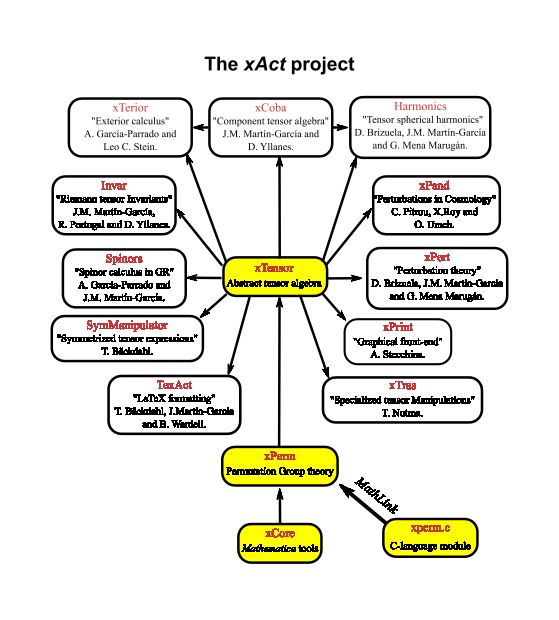
See www.xact.es
                                     -Graphics-

Figure credit: Alfonso Garcia-Parrado Gomez-Loboa and Jose M. Martin-Garcia,  Comput. Phys. Commun. 183 (2012) 2214-2225;
Modified by Barry Wardell

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Load xTensor

Three different notations to load a package (use only one of them!)

<< xAct/xTensor/xTensor.m

Needs[“xAct`xTensor`”]

<< xAct`xTensor`

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
?xAct`xTensor`*
```

```mathematica
?xAct`xTensor`Metric
```

```mathematica
?Metric
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## The Mathematical Structure

Hierarchy of objects:

```mathematica
Manifold

				  Vector Bundle (VBundle)

					 	Tensor

			        	Connection (CovD)

                                                      Metric
```

Types in xTensor are defined through inquiring functions. For a given Type there are four associated objects:

```mathematica
DefType[object, properties]
```

```mathematica
UndefType[object]
```

```mathematica
TypeQ[object]^=True;
```

```mathematica
$Types
```

Currently, these types can be defined in xTensor.

```mathematica
?xAct`xTensor`Def*
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Define Manifolds

Define a constant

```mathematica
DefConstantSymbol[dimension,PrintAs->"n"]
```

** DefConstantSymbol: Defining constant symbol dimension.

```mathematica
dimension
```

n

```mathematica
n//FullForm
```

dimension

```mathematica
?DefConstantSymbol
```

```mathematica
?PrintAs
```

Define a Manifold

```mathematica
DefManifold[M,dimension,Complement[IndexRange[a,q],{g,h,n}]]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
IndexRange[a,q]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q}

```mathematica
Complement[IndexRange[a,q],{g,h,n}]
```

{a,b,c,d,e,f,i,j,k,l,m,o,p,q}

```mathematica
$AbstractIndices
```

{a,b,c,d,e,f,i,j,k,l,m,o,p,q}

```mathematica
?$AbstractIndices
```

```mathematica
?M
```

```mathematica
DefInfo[M]
```

{manifold,}

```mathematica
DefManifold[Mtest,dimension,IndexRange[α,ν]]
```

** DefManifold: Defining manifold Mtest.

** DefVBundle: Defining vbundle TangentMtest.

```mathematica
$AbstractIndices
```

{a,b,c,d,e,f,i,j,k,l,m,o,p,q,α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν}

```mathematica
$Manifolds
```

{M,Mtest}

```mathematica
UndefManifold@Mtest
```

** UndefVBundle: Undefined vbundle 𝕋Mtest

** UndefManifold: Undefined manifold Mtest

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Define Tensors

Define a contravariant vector field:

```mathematica
DefTensor[v[b],M]
v[b]
```

** DefTensor: Defining tensor v[b].

v | b

Define a covariant vector field

```mathematica
DefTensor[w[-b],M]
w[-b]
```

** DefTensor: Defining tensor w[-b].

w |  
b

Define an antisymmmetric tensor field

```mathematica
DefTensor[F[-b,-c],M,Antisymmetric[{-b,-c}]]
```

** DefTensor: Defining tensor F[-b,-c].

```mathematica
F[-c,-b]
%//ToCanonical
```

F |   |  
c | b

-F |   |  
b | c

```mathematica
?ToCanonical
```

```mathematica
F[-b,-c]*v[b]*v[c]
```

F |   |  
b | c v | b
  v | c

```mathematica
%//ToCanonical
```

0

Define a symmmetric tensor field

```mathematica
DefTensor[S[a,b],M,Symmetric[{a,b}]]
```

** DefTensor: Defining tensor S[a,b].

```mathematica
F[-a,-b]*S[a,b]
```

F |   |  
a | b S | a | b
  |

```mathematica
%//ToCanonical
```

0

Dummies:

```mathematica
expr=F[-a,-d]*v[d]*v[b]*v[-b]+3v[b]*v[c]*v[-c]*F[-b,d]*F[-d,-a]
```

3 F |   | d
b |   F |   |  
d | a v | b
  v |  
c v | c
 +F |   |  
a | d v |  
b v | b
  v | d

```mathematica
ToCanonical[expr]
```

F |   |  
a | c v |  
b v | b
  v | c
 -3 F |   |  
a | d F |   | d
c |   v |  
b v | b
  v | c

```mathematica
Simplify[%]
```

(F |   |  
a | c-3 F |   |  
a | d F |   | d
c |  ) v |  
b v | b
  v | c

Validation:

```mathematica
expr
```

3 F |   | d
b |   F |   |  
d | a v | b
  v |  
c v | c
 +F |   |  
a | d v |  
b v | b
  v | d

```mathematica
%//Validate
```

Validate::error: Invalid character of index in tensor F

Validate::error: Invalid character of index in tensor v

General::stop: Further output of Validate::error will be suppressed during this calculation.

3 ERROR[F |   | d
b |  ] ERROR[v |  
c] F |   |  
d | a v | b
  v | c
 +ERROR[v |  
b] F |   |  
a | d v | b
  v | d

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Define Connections

A covd ▽ is an operator obeying (Wald, chapter 2):
	1) ▽[ x + y ]  =  ▽[ x ] + ▽[ y ]
	2) ▽[ x y ] = ▽[ x ] y + x ▽[ y ]
	3) ▽[ f ] = df	for any scalar field f
	4) Commutativity with index contraction

Define an arbitrary connection :

```mathematica
DefCovD[cd[-a],Torsion->True,{"|","𝔇"}]
```

** DefCovD: Defining covariant derivative cd[-a].

** DefTensor: Defining torsion tensor Torsioncd[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor Christoffelcd[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanncd[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor Riccicd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

Commutation now gives torsion tensors as well as Riemann tensors :

```mathematica
expr1=cd[-a]@cd[-b]@Riccicd[-c,-d]
```

𝔇_a 𝔇_b R[𝔇] |   |  
c | d

```mathematica
$CovDFormat="Postfix";
```

```mathematica
expr1
```

R[𝔇] |   |   |    |   
c | d | |b | |a

```mathematica
%//SortCovDs
```

-R[𝔇] |   |  
q$13887 | d R[𝔇] |   |   |   | q$13887
b | a | c |  -R[𝔇] |   |  
c | q$13887 R[𝔇] |   |   |   | q$13887
b | a | d |  +R[𝔇] |   |   |    |   
c | d | |a | |b+T[𝔇] | q$13888 |   |  
  | b | a R[𝔇] |   |   |   
c | d | |q$13888

Hide away dollar-indices.

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
%%
```

-R[𝔇] |   |  
e | d R[𝔇] |   |   |   | e
b | a | c |  -R[𝔇] |   |  
c | e R[𝔇] |   |   |   | e
b | a | d |  +R[𝔇] |   |   |    |   
c | d | |a | |b+T[𝔇] | e |   |  
  | b | a R[𝔇] |   |   |   
c | d | |e

```mathematica
?SortCovDs
```

SortCovDs[expr, covd] exchange repeatedly two instances of the covariant derivative covd, introducing Riemann tensors if needed, until the indices of the derivatives are sorted in canonical order.

```mathematica
$CovDFormat="Prefix";
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## The "fiducial" Derivative

There is a predefined derivative called PD, with zero torsion and curvature ("ordinary" in Wald's terminology) :

```mathematica
$Tensors
```

{v,w,F,S,Torsioncd,Christoffelcd,Riemanncd,Riccicd}

```mathematica
PD[-a]@ F[b,-c]
```

∂_a F | b |  
  | c

```mathematica
PD[-a]@PD[-b]@F[c,-d]
```

∂_a ∂_b F | c |  
  | d

```mathematica
PD[-a][ PD[-b][ F[c,-d] ] ]
```

∂_a ∂_b F | c |  
  | d

```mathematica
SortCovDs[%]
```

∂_b ∂_a F | c |  
  | d

Christoffel tensors are always the "difference" between a given arbitrary connection and PD.

```mathematica
Christoffelcd[a,-b,-c]
```

Γ[𝔇] | a |   |  
  | b | c

```mathematica
cd[-a][v[b]]
```

𝔇_a v | b

```mathematica
ChangeCovD[cd[-a][v[b]],cd,PD]
```

Γ[𝔇] | b |   |  
  | a | c v | c
 +∂_a v | b

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Example 1: First Bianchi Identity

```mathematica
Riemanncd[-a,-b,-c,d]+cd[-a][ Torsioncd[d,-b,-c] ]-Torsioncd[e,-a,-b]Torsioncd[d,-c,-e]
```

R[𝔇] |   |   |   | d
a | b | c |  -T[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | a | b+𝔇_a T[𝔇] | d |   |  
  | b | c

We want to prove that R_[abc]^d-(T^e)_([ab)(T^d)_(c]e)+D_([a)(T^d)_(bc])=0.

```mathematica
Antisymmetrize[%,{-a,-b,-c}]
```

1/6 (R[𝔇] |   |   |   | d
a | b | c |  -R[𝔇] |   |   |   | d
a | c | b |  -R[𝔇] |   |   |   | d
b | a | c |  +R[𝔇] |   |   |   | d
b | c | a |  +R[𝔇] |   |   |   | d
c | a | b |  -R[𝔇] |   |   |   | d
c | b | a |  -T[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | a | b+T[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | a | c+T[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | b | a-T[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | b | c-T[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | c | a+T[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | c | b+𝔇_a T[𝔇] | d |   |  
  | b | c-𝔇_a T[𝔇] | d |   |  
  | c | b-𝔇_b T[𝔇] | d |   |  
  | a | c+𝔇_b T[𝔇] | d |   |  
  | c | a+𝔇_c T[𝔇] | d |   |  
  | a | b-𝔇_c T[𝔇] | d |   |  
  | b | a)

That is zero for any covariant derivative. Let us show it.

```mathematica
6*%//CovDToChristoffel
```

R[𝔇] |   |   |   | d
a | b | c |  -R[𝔇] |   |   |   | d
a | c | b |  -R[𝔇] |   |   |   | d
b | a | c |  +R[𝔇] |   |   |   | d
b | c | a |  +R[𝔇] |   |   |   | d
c | a | b |  -R[𝔇] |   |   |   | d
c | b | a |  +Γ[𝔇] | e |   |  
  | b | c T[𝔇] | d |   |  
  | a | e-Γ[𝔇] | e |   |  
  | c | b T[𝔇] | d |   |  
  | a | e-Γ[𝔇] | e |   |  
  | a | c T[𝔇] | d |   |  
  | b | e+Γ[𝔇] | e |   |  
  | c | a T[𝔇] | d |   |  
  | b | e+Γ[𝔇] | e |   |  
  | a | b T[𝔇] | d |   |  
  | c | e-Γ[𝔇] | e |   |  
  | b | a T[𝔇] | d |   |  
  | c | e-Γ[𝔇] | e |   |  
  | b | c T[𝔇] | d |   |  
  | e | a+Γ[𝔇] | e |   |  
  | c | b T[𝔇] | d |   |  
  | e | a+Γ[𝔇] | e |   |  
  | a | c T[𝔇] | d |   |  
  | e | b-Γ[𝔇] | e |   |  
  | c | a T[𝔇] | d |   |  
  | e | b-Γ[𝔇] | e |   |  
  | a | b T[𝔇] | d |   |  
  | e | c+Γ[𝔇] | e |   |  
  | b | a T[𝔇] | d |   |  
  | e | c+Γ[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | a | b-T[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | a | b-Γ[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | a | c+T[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | a | c-Γ[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | b | a+T[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | b | a+Γ[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | b | c-T[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | b | c+Γ[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | c | a-T[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | c | a-Γ[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | c | b+T[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | c | b+∂_a T[𝔇] | d |   |  
  | b | c-∂_a T[𝔇] | d |   |  
  | c | b-∂_b T[𝔇] | d |   |  
  | a | c+∂_b T[𝔇] | d |   |  
  | c | a+∂_c T[𝔇] | d |   |  
  | a | b-∂_c T[𝔇] | d |   |  
  | b | a

```mathematica
%//RiemannToChristoffel
```

-2 Γ[𝔇] | d |   |  
  | c | e Γ[𝔇] | e |   |  
  | a | b+2 Γ[𝔇] | d |   |  
  | b | e Γ[𝔇] | e |   |  
  | a | c+2 Γ[𝔇] | d |   |  
  | c | e Γ[𝔇] | e |   |  
  | b | a-2 Γ[𝔇] | d |   |  
  | a | e Γ[𝔇] | e |   |  
  | b | c-2 Γ[𝔇] | d |   |  
  | b | e Γ[𝔇] | e |   |  
  | c | a+2 Γ[𝔇] | d |   |  
  | a | e Γ[𝔇] | e |   |  
  | c | b+Γ[𝔇] | e |   |  
  | b | c T[𝔇] | d |   |  
  | a | e-Γ[𝔇] | e |   |  
  | c | b T[𝔇] | d |   |  
  | a | e-Γ[𝔇] | e |   |  
  | a | c T[𝔇] | d |   |  
  | b | e+Γ[𝔇] | e |   |  
  | c | a T[𝔇] | d |   |  
  | b | e+Γ[𝔇] | e |   |  
  | a | b T[𝔇] | d |   |  
  | c | e-Γ[𝔇] | e |   |  
  | b | a T[𝔇] | d |   |  
  | c | e-Γ[𝔇] | e |   |  
  | b | c T[𝔇] | d |   |  
  | e | a+Γ[𝔇] | e |   |  
  | c | b T[𝔇] | d |   |  
  | e | a+Γ[𝔇] | e |   |  
  | a | c T[𝔇] | d |   |  
  | e | b-Γ[𝔇] | e |   |  
  | c | a T[𝔇] | d |   |  
  | e | b-Γ[𝔇] | e |   |  
  | a | b T[𝔇] | d |   |  
  | e | c+Γ[𝔇] | e |   |  
  | b | a T[𝔇] | d |   |  
  | e | c+Γ[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | a | b-T[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | a | b-Γ[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | a | c+T[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | a | c-Γ[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | b | a+T[𝔇] | d |   |  
  | c | e T[𝔇] | e |   |  
  | b | a+Γ[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | b | c-T[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | b | c+Γ[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | c | a-T[𝔇] | d |   |  
  | b | e T[𝔇] | e |   |  
  | c | a-Γ[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | c | b+T[𝔇] | d |   |  
  | a | e T[𝔇] | e |   |  
  | c | b-2 ∂_a Γ[𝔇] | d |   |  
  | b | c+2 ∂_a Γ[𝔇] | d |   |  
  | c | b+∂_a T[𝔇] | d |   |  
  | b | c-∂_a T[𝔇] | d |   |  
  | c | b+2 ∂_b Γ[𝔇] | d |   |  
  | a | c-2 ∂_b Γ[𝔇] | d |   |  
  | c | a-∂_b T[𝔇] | d |   |  
  | a | c+∂_b T[𝔇] | d |   |  
  | c | a-2 ∂_c Γ[𝔇] | d |   |  
  | a | b+2 ∂_c Γ[𝔇] | d |   |  
  | b | a+∂_c T[𝔇] | d |   |  
  | a | b-∂_c T[𝔇] | d |   |  
  | b | a

```mathematica
%//TorsionToChristoffel
```

-2 Γ[𝔇] | d |   |  
  | c | e Γ[𝔇] | e |   |  
  | a | b+(Γ[𝔇] | d |   |  
  | c | e-Γ[𝔇] | d |   |  
  | e | c) Γ[𝔇] | e |   |  
  | a | b-(-Γ[𝔇] | d |   |  
  | c | e+Γ[𝔇] | d |   |  
  | e | c) Γ[𝔇] | e |   |  
  | a | b+2 Γ[𝔇] | d |   |  
  | b | e Γ[𝔇] | e |   |  
  | a | c-(Γ[𝔇] | d |   |  
  | b | e-Γ[𝔇] | d |   |  
  | e | b) Γ[𝔇] | e |   |  
  | a | c+(-Γ[𝔇] | d |   |  
  | b | e+Γ[𝔇] | d |   |  
  | e | b) Γ[𝔇] | e |   |  
  | a | c+Γ[𝔇] | d |   |  
  | c | e (Γ[𝔇] | e |   |  
  | a | b-Γ[𝔇] | e |   |  
  | b | a)-(Γ[𝔇] | d |   |  
  | c | e-Γ[𝔇] | d |   |  
  | e | c) (Γ[𝔇] | e |   |  
  | a | b-Γ[𝔇] | e |   |  
  | b | a)+2 Γ[𝔇] | d |   |  
  | c | e Γ[𝔇] | e |   |  
  | b | a-(Γ[𝔇] | d |   |  
  | c | e-Γ[𝔇] | d |   |  
  | e | c) Γ[𝔇] | e |   |  
  | b | a+(-Γ[𝔇] | d |   |  
  | c | e+Γ[𝔇] | d |   |  
  | e | c) Γ[𝔇] | e |   |  
  | b | a-Γ[𝔇] | d |   |  
  | c | e (-Γ[𝔇] | e |   |  
  | a | b+Γ[𝔇] | e |   |  
  | b | a)+(Γ[𝔇] | d |   |  
  | c | e-Γ[𝔇] | d |   |  
  | e | c) (-Γ[𝔇] | e |   |  
  | a | b+Γ[𝔇] | e |   |  
  | b | a)-2 Γ[𝔇] | d |   |  
  | a | e Γ[𝔇] | e |   |  
  | b | c+(Γ[𝔇] | d |   |  
  | a | e-Γ[𝔇] | d |   |  
  | e | a) Γ[𝔇] | e |   |  
  | b | c-(-Γ[𝔇] | d |   |  
  | a | e+Γ[𝔇] | d |   |  
  | e | a) Γ[𝔇] | e |   |  
  | b | c-Γ[𝔇] | d |   |  
  | b | e (Γ[𝔇] | e |   |  
  | a | c-Γ[𝔇] | e |   |  
  | c | a)+(Γ[𝔇] | d |   |  
  | b | e-Γ[𝔇] | d |   |  
  | e | b) (Γ[𝔇] | e |   |  
  | a | c-Γ[𝔇] | e |   |  
  | c | a)-2 Γ[𝔇] | d |   |  
  | b | e Γ[𝔇] | e |   |  
  | c | a+(Γ[𝔇] | d |   |  
  | b | e-Γ[𝔇] | d |   |  
  | e | b) Γ[𝔇] | e |   |  
  | c | a-(-Γ[𝔇] | d |   |  
  | b | e+Γ[𝔇] | d |   |  
  | e | b) Γ[𝔇] | e |   |  
  | c | a+Γ[𝔇] | d |   |  
  | b | e (-Γ[𝔇] | e |   |  
  | a | c+Γ[𝔇] | e |   |  
  | c | a)-(Γ[𝔇] | d |   |  
  | b | e-Γ[𝔇] | d |   |  
  | e | b) (-Γ[𝔇] | e |   |  
  | a | c+Γ[𝔇] | e |   |  
  | c | a)+Γ[𝔇] | d |   |  
  | a | e (Γ[𝔇] | e |   |  
  | b | c-Γ[𝔇] | e |   |  
  | c | b)-(Γ[𝔇] | d |   |  
  | a | e-Γ[𝔇] | d |   |  
  | e | a) (Γ[𝔇] | e |   |  
  | b | c-Γ[𝔇] | e |   |  
  | c | b)+2 Γ[𝔇] | d |   |  
  | a | e Γ[𝔇] | e |   |  
  | c | b-(Γ[𝔇] | d |   |  
  | a | e-Γ[𝔇] | d |   |  
  | e | a) Γ[𝔇] | e |   |  
  | c | b+(-Γ[𝔇] | d |   |  
  | a | e+Γ[𝔇] | d |   |  
  | e | a) Γ[𝔇] | e |   |  
  | c | b-Γ[𝔇] | d |   |  
  | a | e (-Γ[𝔇] | e |   |  
  | b | c+Γ[𝔇] | e |   |  
  | c | b)+(Γ[𝔇] | d |   |  
  | a | e-Γ[𝔇] | d |   |  
  | e | a) (-Γ[𝔇] | e |   |  
  | b | c+Γ[𝔇] | e |   |  
  | c | b)

```mathematica
%//ToCanonical
```

0

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Example 2: Second Bianchi Identity

```mathematica
cd[-a][ Riemanncd[-b,-c,-d,e] ]-Torsioncd[f,-a,-b]Riemanncd[-c,-f,-d,e]
```

-R[𝔇] |   |   |   | e
c | f | d |   T[𝔇] | f |   |  
  | a | b+𝔇_a R[𝔇] |   |   |   | e
b | c | d |

We want to prove that -(T^f)_([ab)(R_(c]fd))^e+D_([a)(R_(bc]d))^e=0.

```mathematica
Antisymmetrize[%,{-a,-b,-c}]
```

1/6 (-R[𝔇] |   |   |   | e
c | f | d |   T[𝔇] | f |   |  
  | a | b+R[𝔇] |   |   |   | e
b | f | d |   T[𝔇] | f |   |  
  | a | c+R[𝔇] |   |   |   | e
c | f | d |   T[𝔇] | f |   |  
  | b | a-R[𝔇] |   |   |   | e
a | f | d |   T[𝔇] | f |   |  
  | b | c-R[𝔇] |   |   |   | e
b | f | d |   T[𝔇] | f |   |  
  | c | a+R[𝔇] |   |   |   | e
a | f | d |   T[𝔇] | f |   |  
  | c | b+𝔇_a R[𝔇] |   |   |   | e
b | c | d |  -𝔇_a R[𝔇] |   |   |   | e
c | b | d |  -𝔇_b R[𝔇] |   |   |   | e
a | c | d |  +𝔇_b R[𝔇] |   |   |   | e
c | a | d |  +𝔇_c R[𝔇] |   |   |   | e
a | b | d |  -𝔇_c R[𝔇] |   |   |   | e
b | a | d |  )

That is zero for any covariant derivative. Let us show it.

```mathematica
6*%//CovDToChristoffel
```

Γ[𝔇] | e |   |  
  | c | f R[𝔇] |   |   |   | f
a | b | d |  -Γ[𝔇] | f |   |  
  | c | d R[𝔇] |   |   |   | e
a | b | f |  -Γ[𝔇] | e |   |  
  | b | f R[𝔇] |   |   |   | f
a | c | d |  +Γ[𝔇] | f |   |  
  | b | d R[𝔇] |   |   |   | e
a | c | f |  +Γ[𝔇] | f |   |  
  | b | c R[𝔇] |   |   |   | e
a | f | d |  -Γ[𝔇] | f |   |  
  | c | b R[𝔇] |   |   |   | e
a | f | d |  -Γ[𝔇] | e |   |  
  | c | f R[𝔇] |   |   |   | f
b | a | d |  +Γ[𝔇] | f |   |  
  | c | d R[𝔇] |   |   |   | e
b | a | f |  +Γ[𝔇] | e |   |  
  | a | f R[𝔇] |   |   |   | f
b | c | d |  -Γ[𝔇] | f |   |  
  | a | d R[𝔇] |   |   |   | e
b | c | f |  -Γ[𝔇] | f |   |  
  | a | c R[𝔇] |   |   |   | e
b | f | d |  +Γ[𝔇] | f |   |  
  | c | a R[𝔇] |   |   |   | e
b | f | d |  +Γ[𝔇] | e |   |  
  | b | f R[𝔇] |   |   |   | f
c | a | d |  -Γ[𝔇] | f |   |  
  | b | d R[𝔇] |   |   |   | e
c | a | f |  -Γ[𝔇] | e |   |  
  | a | f R[𝔇] |   |   |   | f
c | b | d |  +Γ[𝔇] | f |   |  
  | a | d R[𝔇] |   |   |   | e
c | b | f |  +Γ[𝔇] | f |   |  
  | a | b R[𝔇] |   |   |   | e
c | f | d |  -Γ[𝔇] | f |   |  
  | b | a R[𝔇] |   |   |   | e
c | f | d |  -Γ[𝔇] | f |   |  
  | b | c R[𝔇] |   |   |   | e
f | a | d |  +Γ[𝔇] | f |   |  
  | c | b R[𝔇] |   |   |   | e
f | a | d |  +Γ[𝔇] | f |   |  
  | a | c R[𝔇] |   |   |   | e
f | b | d |  -Γ[𝔇] | f |   |  
  | c | a R[𝔇] |   |   |   | e
f | b | d |  -Γ[𝔇] | f |   |  
  | a | b R[𝔇] |   |   |   | e
f | c | d |  +Γ[𝔇] | f |   |  
  | b | a R[𝔇] |   |   |   | e
f | c | d |  -R[𝔇] |   |   |   | e
c | f | d |   T[𝔇] | f |   |  
  | a | b+R[𝔇] |   |   |   | e
b | f | d |   T[𝔇] | f |   |  
  | a | c+R[𝔇] |   |   |   | e
c | f | d |   T[𝔇] | f |   |  
  | b | a-R[𝔇] |   |   |   | e
a | f | d |   T[𝔇] | f |   |  
  | b | c-R[𝔇] |   |   |   | e
b | f | d |   T[𝔇] | f |   |  
  | c | a+R[𝔇] |   |   |   | e
a | f | d |   T[𝔇] | f |   |  
  | c | b+∂_a R[𝔇] |   |   |   | e
b | c | d |  -∂_a R[𝔇] |   |   |   | e
c | b | d |  -∂_b R[𝔇] |   |   |   | e
a | c | d |  +∂_b R[𝔇] |   |   |   | e
c | a | d |  +∂_c R[𝔇] |   |   |   | e
a | b | d |  -∂_c R[𝔇] |   |   |   | e
b | a | d |

```mathematica
%//RiemannToChristoffel
```

-2 Γ[𝔇] | f |   |  
  | c | d ∂_a Γ[𝔇] | e |   |  
  | b | f+2 Γ[𝔇] | f |   |  
  | b | d ∂_a Γ[𝔇] | e |   |  
  | c | f+2 Γ[𝔇] | e |   |  
  | c | f ∂_a Γ[𝔇] | f |   |  
  | b | d-2 Γ[𝔇] | e |   |  
  | b | f ∂_a Γ[𝔇] | f |   |  
  | c | d-2 ∂_a ∂_b Γ[𝔇] | e |   |  
  | c | d+2 ∂_a ∂_c Γ[𝔇] | e |   |  
  | b | d+Γ[𝔇] | f |   |  
  | c | d (-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | a | f+Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | b | f+∂_a Γ[𝔇] | e |   |  
  | b | f-∂_b Γ[𝔇] | e |   |  
  | a | f)+2 Γ[𝔇] | f |   |  
  | c | d ∂_b Γ[𝔇] | e |   |  
  | a | f-Γ[𝔇] | f |   |  
  | c | d (Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | a | f-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | b | f-∂_a Γ[𝔇] | e |   |  
  | b | f+∂_b Γ[𝔇] | e |   |  
  | a | f)-2 Γ[𝔇] | f |   |  
  | a | d ∂_b Γ[𝔇] | e |   |  
  | c | f-Γ[𝔇] | e |   |  
  | c | f (-Γ[𝔇] | f |   |  
  | b | i Γ[𝔇] | i |   |  
  | a | d+Γ[𝔇] | f |   |  
  | a | i Γ[𝔇] | i |   |  
  | b | d+∂_a Γ[𝔇] | f |   |  
  | b | d-∂_b Γ[𝔇] | f |   |  
  | a | d)-2 Γ[𝔇] | e |   |  
  | c | f ∂_b Γ[𝔇] | f |   |  
  | a | d+Γ[𝔇] | e |   |  
  | c | f (Γ[𝔇] | f |   |  
  | b | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | f |   |  
  | a | i Γ[𝔇] | i |   |  
  | b | d-∂_a Γ[𝔇] | f |   |  
  | b | d+∂_b Γ[𝔇] | f |   |  
  | a | d)+2 Γ[𝔇] | e |   |  
  | a | f ∂_b Γ[𝔇] | f |   |  
  | c | d+2 ∂_b ∂_a Γ[𝔇] | e |   |  
  | c | d-2 ∂_b ∂_c Γ[𝔇] | e |   |  
  | a | d-Γ[𝔇] | f |   |  
  | b | d (-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | a | f+Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | c | f+∂_a Γ[𝔇] | e |   |  
  | c | f-∂_c Γ[𝔇] | e |   |  
  | a | f)-2 Γ[𝔇] | f |   |  
  | b | d ∂_c Γ[𝔇] | e |   |  
  | a | f+Γ[𝔇] | f |   |  
  | b | d (Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | a | f-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | c | f-∂_a Γ[𝔇] | e |   |  
  | c | f+∂_c Γ[𝔇] | e |   |  
  | a | f)+Γ[𝔇] | f |   |  
  | a | d (-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | b | f+Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | c | f+∂_b Γ[𝔇] | e |   |  
  | c | f-∂_c Γ[𝔇] | e |   |  
  | b | f)+2 Γ[𝔇] | f |   |  
  | a | d ∂_c Γ[𝔇] | e |   |  
  | b | f-Γ[𝔇] | f |   |  
  | a | d (Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | b | f-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | c | f-∂_b Γ[𝔇] | e |   |  
  | c | f+∂_c Γ[𝔇] | e |   |  
  | b | f)+Γ[𝔇] | e |   |  
  | b | f (-Γ[𝔇] | f |   |  
  | c | i Γ[𝔇] | i |   |  
  | a | d+Γ[𝔇] | f |   |  
  | a | i Γ[𝔇] | i |   |  
  | c | d+∂_a Γ[𝔇] | f |   |  
  | c | d-∂_c Γ[𝔇] | f |   |  
  | a | d)+2 Γ[𝔇] | e |   |  
  | b | f ∂_c Γ[𝔇] | f |   |  
  | a | d-Γ[𝔇] | e |   |  
  | b | f (Γ[𝔇] | f |   |  
  | c | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | f |   |  
  | a | i Γ[𝔇] | i |   |  
  | c | d-∂_a Γ[𝔇] | f |   |  
  | c | d+∂_c Γ[𝔇] | f |   |  
  | a | d)-Γ[𝔇] | e |   |  
  | a | f (-Γ[𝔇] | f |   |  
  | c | i Γ[𝔇] | i |   |  
  | b | d+Γ[𝔇] | f |   |  
  | b | i Γ[𝔇] | i |   |  
  | c | d+∂_b Γ[𝔇] | f |   |  
  | c | d-∂_c Γ[𝔇] | f |   |  
  | b | d)-2 Γ[𝔇] | e |   |  
  | a | f ∂_c Γ[𝔇] | f |   |  
  | b | d+Γ[𝔇] | e |   |  
  | a | f (Γ[𝔇] | f |   |  
  | c | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | f |   |  
  | b | i Γ[𝔇] | i |   |  
  | c | d-∂_b Γ[𝔇] | f |   |  
  | c | d+∂_c Γ[𝔇] | f |   |  
  | b | d)-2 ∂_c ∂_a Γ[𝔇] | e |   |  
  | b | d+2 ∂_c ∂_b Γ[𝔇] | e |   |  
  | a | d-Γ[𝔇] | f |   |  
  | b | c (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d+Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d+∂_a Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | a | d)+Γ[𝔇] | f |   |  
  | c | b (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d+Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d+∂_a Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | a | d)+Γ[𝔇] | f |   |  
  | b | c (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d-∂_a Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | a | d)-Γ[𝔇] | f |   |  
  | c | b (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d-∂_a Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | a | d)-T[𝔇] | f |   |  
  | b | c (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d-∂_a Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | a | d)+T[𝔇] | f |   |  
  | c | b (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d-∂_a Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | a | d)+Γ[𝔇] | f |   |  
  | a | c (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d+Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d+∂_b Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | b | d)-Γ[𝔇] | f |   |  
  | c | a (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d+Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d+∂_b Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | b | d)-Γ[𝔇] | f |   |  
  | a | c (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d-∂_b Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | b | d)+Γ[𝔇] | f |   |  
  | c | a (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d-∂_b Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | b | d)+T[𝔇] | f |   |  
  | a | c (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d-∂_b Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | b | d)-T[𝔇] | f |   |  
  | c | a (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d-∂_b Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | b | d)-Γ[𝔇] | f |   |  
  | a | b (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d+Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d+∂_c Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | c | d)+Γ[𝔇] | f |   |  
  | b | a (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d+Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d+∂_c Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | c | d)+Γ[𝔇] | f |   |  
  | a | b (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d-∂_c Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | c | d)-Γ[𝔇] | f |   |  
  | b | a (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d-∂_c Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | c | d)-T[𝔇] | f |   |  
  | a | b (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d-∂_c Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | c | d)+T[𝔇] | f |   |  
  | b | a (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d-∂_c Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | c | d)

```mathematica
%//TorsionToChristoffel
```

-2 Γ[𝔇] | f |   |  
  | c | d ∂_a Γ[𝔇] | e |   |  
  | b | f+2 Γ[𝔇] | f |   |  
  | b | d ∂_a Γ[𝔇] | e |   |  
  | c | f+2 Γ[𝔇] | e |   |  
  | c | f ∂_a Γ[𝔇] | f |   |  
  | b | d-2 Γ[𝔇] | e |   |  
  | b | f ∂_a Γ[𝔇] | f |   |  
  | c | d-2 ∂_a ∂_b Γ[𝔇] | e |   |  
  | c | d+2 ∂_a ∂_c Γ[𝔇] | e |   |  
  | b | d+Γ[𝔇] | f |   |  
  | c | d (-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | a | f+Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | b | f+∂_a Γ[𝔇] | e |   |  
  | b | f-∂_b Γ[𝔇] | e |   |  
  | a | f)+2 Γ[𝔇] | f |   |  
  | c | d ∂_b Γ[𝔇] | e |   |  
  | a | f-Γ[𝔇] | f |   |  
  | c | d (Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | a | f-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | b | f-∂_a Γ[𝔇] | e |   |  
  | b | f+∂_b Γ[𝔇] | e |   |  
  | a | f)-2 Γ[𝔇] | f |   |  
  | a | d ∂_b Γ[𝔇] | e |   |  
  | c | f-Γ[𝔇] | e |   |  
  | c | f (-Γ[𝔇] | f |   |  
  | b | i Γ[𝔇] | i |   |  
  | a | d+Γ[𝔇] | f |   |  
  | a | i Γ[𝔇] | i |   |  
  | b | d+∂_a Γ[𝔇] | f |   |  
  | b | d-∂_b Γ[𝔇] | f |   |  
  | a | d)-2 Γ[𝔇] | e |   |  
  | c | f ∂_b Γ[𝔇] | f |   |  
  | a | d+Γ[𝔇] | e |   |  
  | c | f (Γ[𝔇] | f |   |  
  | b | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | f |   |  
  | a | i Γ[𝔇] | i |   |  
  | b | d-∂_a Γ[𝔇] | f |   |  
  | b | d+∂_b Γ[𝔇] | f |   |  
  | a | d)+2 Γ[𝔇] | e |   |  
  | a | f ∂_b Γ[𝔇] | f |   |  
  | c | d+2 ∂_b ∂_a Γ[𝔇] | e |   |  
  | c | d-2 ∂_b ∂_c Γ[𝔇] | e |   |  
  | a | d-Γ[𝔇] | f |   |  
  | b | d (-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | a | f+Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | c | f+∂_a Γ[𝔇] | e |   |  
  | c | f-∂_c Γ[𝔇] | e |   |  
  | a | f)-2 Γ[𝔇] | f |   |  
  | b | d ∂_c Γ[𝔇] | e |   |  
  | a | f+Γ[𝔇] | f |   |  
  | b | d (Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | a | f-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | c | f-∂_a Γ[𝔇] | e |   |  
  | c | f+∂_c Γ[𝔇] | e |   |  
  | a | f)+Γ[𝔇] | f |   |  
  | a | d (-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | b | f+Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | c | f+∂_b Γ[𝔇] | e |   |  
  | c | f-∂_c Γ[𝔇] | e |   |  
  | b | f)+2 Γ[𝔇] | f |   |  
  | a | d ∂_c Γ[𝔇] | e |   |  
  | b | f-Γ[𝔇] | f |   |  
  | a | d (Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | b | f-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | c | f-∂_b Γ[𝔇] | e |   |  
  | c | f+∂_c Γ[𝔇] | e |   |  
  | b | f)+Γ[𝔇] | e |   |  
  | b | f (-Γ[𝔇] | f |   |  
  | c | i Γ[𝔇] | i |   |  
  | a | d+Γ[𝔇] | f |   |  
  | a | i Γ[𝔇] | i |   |  
  | c | d+∂_a Γ[𝔇] | f |   |  
  | c | d-∂_c Γ[𝔇] | f |   |  
  | a | d)+2 Γ[𝔇] | e |   |  
  | b | f ∂_c Γ[𝔇] | f |   |  
  | a | d-Γ[𝔇] | e |   |  
  | b | f (Γ[𝔇] | f |   |  
  | c | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | f |   |  
  | a | i Γ[𝔇] | i |   |  
  | c | d-∂_a Γ[𝔇] | f |   |  
  | c | d+∂_c Γ[𝔇] | f |   |  
  | a | d)-Γ[𝔇] | e |   |  
  | a | f (-Γ[𝔇] | f |   |  
  | c | i Γ[𝔇] | i |   |  
  | b | d+Γ[𝔇] | f |   |  
  | b | i Γ[𝔇] | i |   |  
  | c | d+∂_b Γ[𝔇] | f |   |  
  | c | d-∂_c Γ[𝔇] | f |   |  
  | b | d)-2 Γ[𝔇] | e |   |  
  | a | f ∂_c Γ[𝔇] | f |   |  
  | b | d+Γ[𝔇] | e |   |  
  | a | f (Γ[𝔇] | f |   |  
  | c | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | f |   |  
  | b | i Γ[𝔇] | i |   |  
  | c | d-∂_b Γ[𝔇] | f |   |  
  | c | d+∂_c Γ[𝔇] | f |   |  
  | b | d)-2 ∂_c ∂_a Γ[𝔇] | e |   |  
  | b | d+2 ∂_c ∂_b Γ[𝔇] | e |   |  
  | a | d-Γ[𝔇] | f |   |  
  | b | c (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d+Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d+∂_a Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | a | d)+Γ[𝔇] | f |   |  
  | c | b (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d+Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d+∂_a Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | a | d)+Γ[𝔇] | f |   |  
  | b | c (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d-∂_a Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | a | d)-(Γ[𝔇] | f |   |  
  | b | c-Γ[𝔇] | f |   |  
  | c | b) (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d-∂_a Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | a | d)-Γ[𝔇] | f |   |  
  | c | b (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d-∂_a Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | a | d)+(-Γ[𝔇] | f |   |  
  | b | c+Γ[𝔇] | f |   |  
  | c | b) (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | i Γ[𝔇] | i |   |  
  | f | d-∂_a Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | a | d)+Γ[𝔇] | f |   |  
  | a | c (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d+Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d+∂_b Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | b | d)-Γ[𝔇] | f |   |  
  | c | a (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d+Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d+∂_b Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | b | d)-Γ[𝔇] | f |   |  
  | a | c (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d-∂_b Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | b | d)+(Γ[𝔇] | f |   |  
  | a | c-Γ[𝔇] | f |   |  
  | c | a) (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d-∂_b Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | b | d)+Γ[𝔇] | f |   |  
  | c | a (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d-∂_b Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | b | d)-(-Γ[𝔇] | f |   |  
  | a | c+Γ[𝔇] | f |   |  
  | c | a) (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | i Γ[𝔇] | i |   |  
  | f | d-∂_b Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | b | d)-Γ[𝔇] | f |   |  
  | a | b (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d+Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d+∂_c Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | c | d)+Γ[𝔇] | f |   |  
  | b | a (-Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d+Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d+∂_c Γ[𝔇] | e |   |  
  | f | d-∂_f Γ[𝔇] | e |   |  
  | c | d)+Γ[𝔇] | f |   |  
  | a | b (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d-∂_c Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | c | d)-(Γ[𝔇] | f |   |  
  | a | b-Γ[𝔇] | f |   |  
  | b | a) (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d-∂_c Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | c | d)-Γ[𝔇] | f |   |  
  | b | a (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d-∂_c Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | c | d)+(-Γ[𝔇] | f |   |  
  | a | b+Γ[𝔇] | f |   |  
  | b | a) (Γ[𝔇] | e |   |  
  | f | i Γ[𝔇] | i |   |  
  | c | d-Γ[𝔇] | e |   |  
  | c | i Γ[𝔇] | i |   |  
  | f | d-∂_c Γ[𝔇] | e |   |  
  | f | d+∂_f Γ[𝔇] | e |   |  
  | c | d)

```mathematica
%//ToCanonical
```

0

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## General Christoffels

Following Wald, a Christoffel is a “tensor” relating any two covariant derivatives :

```mathematica
DefTensor[X[a,-b],M]
```

** DefTensor: Defining tensor X[a,-b].

```mathematica
expr2= cd[-a][ X[b,-c] ]
```

𝔇_a X | b |  
  | c

```mathematica
ChangeCovD[expr2,cd,PD]
```

-Γ[𝔇] | d |   |  
  | a | c X | b |  
  | d+Γ[𝔇] | b |   |  
  | a | d X | d |  
  | c+∂_a X | b |  
  | c

```mathematica
expr2//CovDToChristoffel
```

-Γ[𝔇] | d |   |  
  | a | c X | b |  
  | d+Γ[𝔇] | b |   |  
  | a | d X | d |  
  | c+∂_a X | b |  
  | c

Define another connection :

```mathematica
DefCovD[CD[-a],Torsion->True,{";","∇"}]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

```mathematica
expr2
```

𝔇_a X | b |  
  | c

```mathematica
ChangeCovD[expr2,cd,CD]
```

** DefTensor: Defining tensor ChristoffelcdCD[a,-b,-c].

-Γ[𝔇,∇] | d |   |  
  | a | c X | b |  
  | d+Γ[𝔇,∇] | b |   |  
  | a | d X | d |  
  | c+∇_a X | b |  
  | c

```mathematica
ChangeCovD[%,CD,PD]//ToCanonical
```

-Γ[∇] | d |   |  
  | a | c X | b |  
  | d-Γ[𝔇,∇] | d |   |  
  | a | c X | b |  
  | d+Γ[∇] | b |   |  
  | a | d X | d |  
  | c+Γ[𝔇,∇] | b |   |  
  | a | d X | d |  
  | c+∂_a X | b |  
  | c

```mathematica
ChangeCovD[expr2,cd,PD]
```

-Γ[𝔇] | d |   |  
  | a | c X | b |  
  | d+Γ[𝔇] | b |   |  
  | a | d X | d |  
  | c+∂_a X | b |  
  | c

```mathematica
%%-%//ToCanonical
```

Γ[𝔇] | d |   |  
  | a | c X | b |  
  | d-Γ[∇] | d |   |  
  | a | c X | b |  
  | d-Γ[𝔇,∇] | d |   |  
  | a | c X | b |  
  | d-Γ[𝔇] | b |   |  
  | a | d X | d |  
  | c+Γ[∇] | b |   |  
  | a | d X | d |  
  | c+Γ[𝔇,∇] | b |   |  
  | a | d X | d |  
  | c

```mathematica
%//BreakChristoffel
```

Γ[𝔇] | d |   |  
  | a | c X | b |  
  | d-(Γ[𝔇] | d |   |  
  | a | c-Γ[∇] | d |   |  
  | a | c) X | b |  
  | d-Γ[∇] | d |   |  
  | a | c X | b |  
  | d-Γ[𝔇] | b |   |  
  | a | d X | d |  
  | c+(Γ[𝔇] | b |   |  
  | a | d-Γ[∇] | b |   |  
  | a | d) X | d |  
  | c+Γ[∇] | b |   |  
  | a | d X | d |  
  | c

```mathematica
%//ToCanonical
```

0

CovDToChristoffel uses ChangeCogvD to transform every connection into PD.

```mathematica
Riemanncd[-a,-b,-c,d]
```

R[𝔇] |   |   |   | d
a | b | c |

```mathematica
ChangeCurvature[%,cd,CD]
```

Γ[𝔇,∇] | d |   |  
  | b | e Γ[𝔇,∇] | e |   |  
  | a | c-Γ[𝔇,∇] | d |   |  
  | a | e Γ[𝔇,∇] | e |   |  
  | b | c+R[∇] |   |   |   | d
a | b | c |  -Γ[𝔇,∇] | d |   |  
  | e | c T[∇] | e |   |  
  | a | b-∇_a Γ[𝔇,∇] | d |   |  
  | b | c+∇_b Γ[𝔇,∇] | d |   |  
  | a | c

```mathematica
ChangeCurvature[%,CD,cd]
```

2 Γ[𝔇,∇] | d |   |  
  | b | e Γ[𝔇,∇] | e |   |  
  | a | c-2 Γ[𝔇,∇] | d |   |  
  | a | e Γ[𝔇,∇] | e |   |  
  | b | c+R[𝔇] |   |   |   | d
a | b | c |  +Γ[𝔇,∇] | d |   |  
  | e | c T[𝔇] | e |   |  
  | a | b-Γ[𝔇,∇] | d |   |  
  | e | c T[∇] | e |   |  
  | a | b+𝔇_a Γ[𝔇,∇] | d |   |  
  | b | c-𝔇_b Γ[𝔇,∇] | d |   |  
  | a | c-∇_a Γ[𝔇,∇] | d |   |  
  | b | c+∇_b Γ[𝔇,∇] | d |   |  
  | a | c

```mathematica
ChangeCovD[%,CD,cd]
```

-Γ[𝔇,∇] | d |   |  
  | e | c Γ[𝔇,∇] | e |   |  
  | a | b+Γ[𝔇,∇] | d |   |  
  | e | c Γ[𝔇,∇] | e |   |  
  | b | a+R[𝔇] |   |   |   | d
a | b | c |  +Γ[𝔇,∇] | d |   |  
  | e | c T[𝔇] | e |   |  
  | a | b-Γ[𝔇,∇] | d |   |  
  | e | c T[∇] | e |   |  
  | a | b

```mathematica
ChangeTorsion[%,CD,cd]
```

-Γ[𝔇,∇] | d |   |  
  | e | c Γ[𝔇,∇] | e |   |  
  | a | b+Γ[𝔇,∇] | d |   |  
  | e | c Γ[𝔇,∇] | e |   |  
  | b | a+R[𝔇] |   |   |   | d
a | b | c |  +Γ[𝔇,∇] | d |   |  
  | e | c T[𝔇] | e |   |  
  | a | b-Γ[𝔇,∇] | d |   |  
  | e | c (-Γ[𝔇,∇] | e |   |  
  | a | b+Γ[𝔇,∇] | e |   |  
  | b | a+T[𝔇] | e |   |  
  | a | b)

```mathematica
%//ToCanonical
```

R[𝔇] |   |   |   | d
a | b | c |

```mathematica
$CovDs
```

{PD,cd,CD}

```mathematica
UndefCovD/@Complement[$CovDs,{PD}];
```

** UndefTensor: Undefined non-symmetric Christoffel tensor Christoffelcd

** UndefTensor: Undefined tensor ChristoffelcdCD

** UndefTensor: Undefined non-symmetric Ricci tensor Riccicd

** UndefTensor: Undefined Riemann tensor Riemanncd

** UndefTensor: Undefined torsion tensor Torsioncd

** UndefCovD: Undefined covariant derivative cd

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefCovD: Undefined covariant derivative CD

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Define Metrics

Define a contravariant vector field:

```mathematica
$Tensors
```

{v,w,F,S}

```mathematica
UndefTensor/@$Tensors;
```

** UndefTensor: Undefined tensor v

** UndefTensor: Undefined tensor w

** UndefTensor: Undefined tensor F

** UndefTensor: Undefined tensor S

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

```mathematica
v[-a]
```

v |  
a

```mathematica
v[-a]//Validate
```

Validate::error: Invalid character of index in tensor v

ERROR[v |  
a]

Define a metric.

```mathematica
DefMetric[-1,g[-a,-b],gcd,{";","∇"}]
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b].

** DefCovD: Defining covariant derivative gcd[-a].

** DefTensor: Defining vanishing torsion tensor Torsiongcd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelgcd[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanngcd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor Riccigcd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalargcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteingcd[-a,-b].

** DefTensor: Defining Weyl tensor Weylgcd[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRiccigcd[-a,-b].

** DefTensor: Defining Kretschmann scalar Kretschmanngcd[].

** DefCovD:  Computing RiemannToWeylRules for dim dimension

** DefCovD:  Computing RicciToTFRicci for dim dimension

** DefCovD:  Computing RicciToEinsteinRules for dim dimension

** DefTensor: Defining weight +2 density Detg[]. Determinant.

```mathematica
?DefMetric
```

DefMetric[signdet, metric[-a,-b], covd, covdsymbol] defines metric[-a, -b] with signdet 1 or -1 and associates the covariant derivative covd[-a] to it.

```mathematica
Options[DefMetric]
```

{PrintAs→Identity,FlatMetric→False,InducedFrom→Null,ConformalTo→Null,OtherDependencies→{},WeightedWithBasis→Null,epsilonOrientationInBasis:>{AIndex,$epsilonSign},Master→Null,ProtectNewSymbol:>$ProtectNewSymbols,DefInfo→{,}}

```mathematica
UndefMetric@g
```

** UndefTensor: Undefined weight +2 density Detg

** UndefTensor: Undefined symmetric Christoffel tensor Christoffelgcd

** UndefTensor: Undefined symmetric Einstein tensor Einsteingcd

** UndefTensor: Undefined Kretschmann scalar Kretschmanngcd

** UndefTensor: Undefined symmetric Ricci tensor Riccigcd

** UndefTensor: Undefined Ricci scalar RicciScalargcd

** UndefTensor: Undefined Riemann tensor Riemanngcd

** UndefTensor: Undefined symmetric TFRicci tensor TFRiccigcd

** UndefTensor: Undefined torsion tensor Torsiongcd

** UndefTensor: Undefined Weyl tensor Weylgcd

** UndefCovD: Undefined covariant derivative gcd

** UndefTensor: Undefined antisymmetric tensor epsilong

** UndefTensor: Undefined symmetric metric tensor g

```mathematica
$DefInfoQ=False;
```

```mathematica
?$DefInfoQ
```

$DefInfoQ is a boolean global variable controlling whether the info definition messages are printed. By default it is True, but setting it to False deactivates all Def messages.

```mathematica
DefMetric[-1,g[-a,-b],gcd,{";","∇"}]
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b].

** DefCovD: Defining covariant derivative gcd[-a].

** DefTensor: Defining vanishing torsion tensor Torsiongcd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelgcd[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanngcd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor Riccigcd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalargcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteingcd[-a,-b].

** DefTensor: Defining Weyl tensor Weylgcd[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRiccigcd[-a,-b].

** DefTensor: Defining Kretschmann scalar Kretschmanngcd[].

** DefCovD:  Computing RiemannToWeylRules for dim dimension

** DefCovD:  Computing RicciToTFRicci for dim dimension

** DefCovD:  Computing RicciToEinsteinRules for dim dimension

** DefTensor: Defining weight +2 density Detg[]. Determinant.

```mathematica
v[-a]//Validate
```

v |  
a

Expressions :

```mathematica
DefTensor[F[a,b],M,Antisymmetric[{a,b}]]
```

```mathematica
F[a,b]F[-b,-c]F[c,-a]
```

F | a | b
  |   F |   |  
b | c F | c |  
  | a

```mathematica
F[a,b]F[-b,-c]F[c,-a]//ToCanonical
```

0

Verify that gcd is associated to metric g:

```mathematica
gcd[-a]@g[c,d]
```

0

```mathematica
HoldForm[gcd[-a]@g[c,d]]==gcd[-a]@g[c,d]
```

∇_a g | c | d
  |  ==0

```mathematica
?HoldForm
```

expr prints as the expression expr, with expr maintained in an unevaluated form.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Example 3: Geodesic Deviation Equation

Tangent and deviation vectors

```mathematica
DefTensor[u[a],M]
DefTensor[n[a],M]
```

** DefTensor: Defining tensor u[a].

** DefTensor: Defining tensor n[a].

u represents the tangent to a geodesic flow, so

u_^b∇_b (u_^a)==0

We will express this using MakeRule.

```mathematica
uisgeodesic=MakeRule[{u[b]gcd[-b]@u[a], 0},MetricOn->All]
```

{HoldPattern[u | UnderBar[b̲]
  ∇_UnderBar[b̲] u | UnderBar[a̲]
 ]:>Module[{},0],HoldPattern[u |  
UnderBar[b̲] ∇^UnderBar[b̲] u | UnderBar[a̲]
 ]:>Module[{},0]}

n is the deviation vector between 2 nearby geodesics.
u and n form a coordinate basis of a 2 dim sub manifold, therefore their Lie bracket vanishes

[u_^b,n_^b]^a==0

We might use MakeRule to code this condition, but we shall find more convenient to express this in a slightly different way:
expand the Bracket in terms of covariant derivatives and then set the 2 terms equal to each other with MakeRule.

u | b
  n | a |   
  | ;b==n | b
  u | a |   
  | ;b

```mathematica
Bracket[u[b],n[b]][a]//BracketToCovD[#,gcd]&
```

u | b
  ∇_b n | a
 -n | b
  ∇_b u | a

Now we write the LHS and the RHS of eq (3) into MakeRule

```mathematica
zeroliebracket=MakeRule[{{{u, {{b}, {}}}} ∇_b {{n, {{a}, {}}}}, {{n, {{b}, {}}}} ∇_b {{u, {{a}, {}}}}},MetricOn->All]
```

{HoldPattern[u | UnderBar[b̲]
  ∇_UnderBar[b̲] n | UnderBar[a̲]
 ]:>Module[{c,d},(n | c
  ∇_c u | d
 ) g |   | a
d |  ],HoldPattern[u |  
UnderBar[b̲] ∇^UnderBar[b̲] n | UnderBar[a̲]
 ]:>Module[{c,d},(n | c
  ∇_c u | d
 ) g |   | a
d |  ]}

We want to study how neighboring geodesics move against each other.
An apparent manifestation of curvature is the amount of acceleration of the separation vector n.
This is calculated by the second derivative (along u) of n.
Symbolically, we will calculate

u_^c∇_c (u_^a∇_a (n_^b))

So we start by considering the derivative of n along u and use the zeroliebracket rule to convert it in the derivative of u alog n

```mathematica
dnalongu=u[a]gcd[-a]@n[b]/.zeroliebracket
```

n | a
  ∇_a u | b

Let' s derive this another time along u to get the acceleration

```mathematica
d2nalongu=u[c]gcd[-c]@dnalongu
```

u | c
  (∇_a u | b
  ∇_c n | a
 +n | a
  ∇_c ∇_a u | b
 )

We want to commute the order of derivation in the last term

```mathematica
d2nalongu=d2nalongu//SortCovDs//Expand
```

n | a
  R[∇] |   |   |   | b
a | c | d |   u | c
  u | d
 +n | a
  u | c
  ∇_a ∇_c u | b
 +u | c
  ∇_a u | b
  ∇_c n | a

Sorting the covariant derivatives has introduced a curvature term.
The last term of this expression has a derivative of n along u, so we use zeroliebracket rule

```mathematica
d2nalongu=d2nalongu/.zeroliebracket
```

n | a
  R[∇] |   |   |   | b
a | c | d |   u | c
  u | d
 +n | a
  u | c
  ∇_a ∇_c u | b
 +n | c
  ∇_a u | b
  ∇_c u | a

But u is the tangent to a geodesic flow, so

```mathematica
{{u, {{a}, {}}}} ∇_a {{u, {{b}, {}}}}/.uisgeodesic
```

0

```mathematica
u[a]gcd[-a]@u[b]
```

u | a
  ∇_a u | b

And of course , if we derive this result along n, we still get 0

```mathematica
n[c]gcd[-c]@({{u, {{a}, {}}}} ∇_a {{u, {{b}, {}}}} )
```

n | c
  (∇_a u | b
  ∇_c u | a
 +u | a
  ∇_c ∇_a u | b
 )

```mathematica
n[c]gcd[-c]@({{u, {{a}, {}}}} ∇_a {{u, {{b}, {}}}}/.uisgeodesic)
```

0

Therefore the following expression is actually 0

```mathematica
zero=n[c]gcd[-c]@({{u, {{a}, {}}}} ∇_a {{u, {{b}, {}}}} )
```

n | c
  (∇_a u | b
  ∇_c u | a
 +u | a
  ∇_c ∇_a u | b
 )

And we can safely subtract it from d2n

```mathematica
d2nalongu=d2nalongu-zero
```

n | a
  R[∇] |   |   |   | b
a | c | d |   u | c
  u | d
 +n | a
  u | c
  ∇_a ∇_c u | b
 +n | c
  ∇_a u | b
  ∇_c u | a
 -n | c
  (∇_a u | b
  ∇_c u | a
 +u | a
  ∇_c ∇_a u | b
 )

After some simplification

```mathematica
d2nalongu=d2nalongu//Simplification
```

-n | a
  R[∇] | b |   |   |  
  | c | a | d u | c
  u | d

we get the relationship between the acceleration of the separation vector n along u and the curvature of the manifold.

In conclusion u_^c∇_c (u | b
  ∇_b (n | e
 ))+n | a
  R[∇] | e |   |   |  
  | c | a | du | c
  u | d
  ==0 .

This result coincides with Wald:General Relativity eq. 3.3.18 and with the last equation on page 274 of MTW’s “Gravitation”.